# Aufgabe 36 Martin und Krüger

## Aufgabe 36 b)

Plot des Graphen der impliziten Funktion:

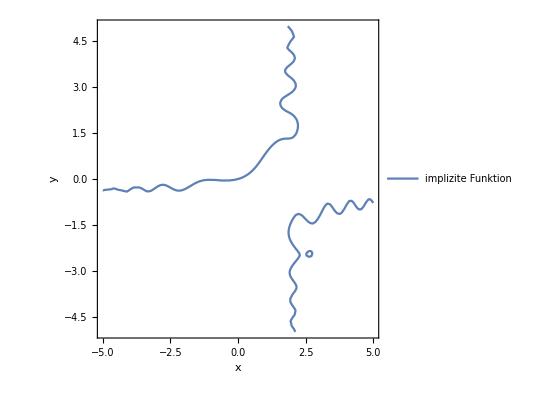

```mathematica
Show[ContourPlot[Sin[x^2]+2x*y+Cos[y^2]+x-4y==1,{x,-5,5},{y,-5,5},FrameLabel->{"x","y"},PlotLegends->{"implizite Funktion"}]]
```

## Aufgabe 36 c)

Berechnung einer beliebigen Ableitung der impliziten Funktion nach y:

```mathematica
derivativesx[depth0_]:=Module[{depth=depth0},
g[c_]:=Solve[D[Sin[x[y]*x[y]]+2x[y]*y+Cos[y^2]+x[y]-4y,{y,c}]==0,D[x[y],{y,c}]];
deriv=List[];

For[l=1,l≤depth,l++,
AppendTo[deriv,g[l][[1,1]]/.deriv]
];
deriv=deriv/.{y->0,x[y]->0}
]
```

Teste die oben definierte Funktion:

```mathematica
derivativesx[10]
```

{x'[0]→4,x''[0]→-48,x^(3)[0]→1440,x^(4)[0]→-71412,x^(5)[0]→4953000,x^(6)[0]→-440993760,x^(7)[0]→47929277760,x^(8)[0]→-6150757843440,x^(9)[0]→910179034783200,x^(10)[0]→-152574372146125440}

Taylorentwicklung nach x[y]:

```mathematica
taylorx[grade_]:=Module[{depth=grade},
g[c_]:=Solve[D[Sin[x[y]*x[y]]+2x[y]*y+Cos[y^2]+x[y]-4y-1,{y,c}]==0,D[x[y],{y,c}]];
deriv=List[];

For[l=1,l≤depth,l++,
AppendTo[deriv,g[l][[1,1]]/.deriv]
];
deriv=Values[deriv/.{y->0,x[y]->0}];
Sum[((Extract[deriv,n])/(n!))*y^n,{n,1,depth}]
]
```

Teste Taylorentwicklung vom Grad 10:

```mathematica
taylorx[10]
```

4 y-24 y^2+240 y^3-(5951 y^4)/2+41275 y^5-(1837474 y^6)/3+(28529332 y^7)/3-(1220388461 y^8)/8+(10032837685 y^9)/4-(420454067863 y^10)/10

Wie man sieht, ist die Taylorentwicklung eine alternierende Reihe. Nach dem Leibniz-Kriterium müssten die Partialsummen notwendigerweise eine Nullfolge bilden. Da y beliebige Werte annehmen kann und die Vorfaktoren jeweils wesentlich größer werden, ist keine Nullfolge vorhanden. Damit konvergiert die Taylorentwicklung nach dem Leibniz-Kriterium nicht. D.h. die Taylorentwicklung divergiert.

## Aufgabe 36 d)

Berechnung einer beliebigen Ableitung der impliziten Funktion nach x:

```mathematica
derivativesy[depth0_]:=Module[{depth=depth0},
g[c_]:=Solve[D[Sin[x*x]+2x*y[x]+Cos[y[x]*y[x]]+x-4y[x],{x,c}]==0,D[y[x],{x,c}]];
deriv=List[];

For[l=1,l≤depth,l++,
AppendTo[deriv,g[l][[1,1]]/.deriv]
];
deriv=deriv/.{x->0,y[x]->0}
]
```

Teste die oben definierte Funktion:

```mathematica
derivativesy[10]
```

{y'[0]→1/4,y''[0]→3/4,y^(3)[0]→9/8,y^(4)[0]→573/256,y^(5)[0]→2685/512,y^(6)[0]→-10275/512,y^(7)[0]→-2299605/16384,y^(8)[0]→-20843235/16384,y^(9)[0]→-398792835/32768,y^(10)[0]→-109839426165/1048576}

Taylorentwicklung nach x[y]:

```mathematica
taylory[grade_]:=Module[{depth=grade},
g[c_]:=Solve[D[Sin[x*x]+2x*y[x]+Cos[y[x]*y[x]]+x-4y[x],{x,c}]==0,D[y[x],{x,c}]];
deriv=List[];

For[l=1,l≤depth,l++,
AppendTo[deriv,g[l][[1,1]]/.deriv]
];
deriv=Values[deriv/.{x->0,y[x]->0}];
Sum[((Extract[deriv,n])/(n!))*x^n,{n,1,depth}]
]
```

Teste Taylorentwicklung vom Grad 10:

```mathematica
taylory[10]
```

x/4+(3 x^2)/8+(3 x^3)/16+(191 x^4)/2048+(179 x^5)/4096-(685 x^6)/24576-(21901 x^7)/786432-(66169 x^8)/2097152-(422003 x^9)/12582912-(116232197 x^10)/4026531840

## Aufgabe 36 e)

Plot der Funktion und der beiden Taylorentwicklungen, jeweils bis zum Grad 5:

```mathematica
taylorx5=taylorx[5]
taylory5=taylory[5]
```

4 y-24 y^2+240 y^3-(5951 y^4)/2+41275 y^5

x/4+(3 x^2)/8+(3 x^3)/16+(191 x^4)/2048+(179 x^5)/4096

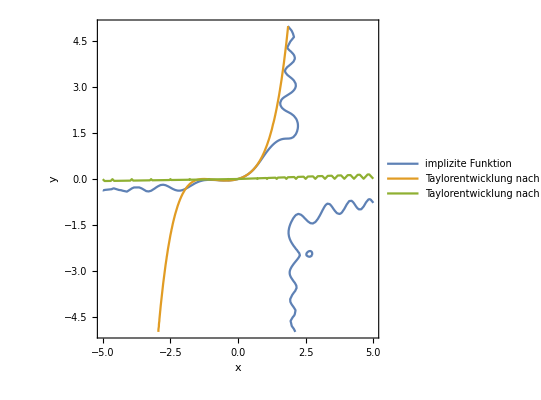

```mathematica
Show[ContourPlot[{Sin[x^2]+2x*y+Cos[y^2]+x-4y==1,taylory5==y,x==taylorx5},{x,-5,5},{y,-5,5},FrameLabel->{"x","y"},PlotLegends->{"implizite Funktion","Taylorentwicklung nach y[x]","Taylorentwicklung nach x[y]"}]]
```

Wobei der Plot der Taylorentwicklungen bis zum Grad 10 wesentlich besser aussieht:

```mathematica
taylorx10=taylorx[10]
taylory10=taylory[10]
```

4 y-24 y^2+240 y^3-(5951 y^4)/2+41275 y^5-(1837474 y^6)/3+(28529332 y^7)/3-(1220388461 y^8)/8+(10032837685 y^9)/4-(420454067863 y^10)/10

x/4+(3 x^2)/8+(3 x^3)/16+(191 x^4)/2048+(179 x^5)/4096-(685 x^6)/24576-(21901 x^7)/786432-(66169 x^8)/2097152-(422003 x^9)/12582912-(116232197 x^10)/4026531840

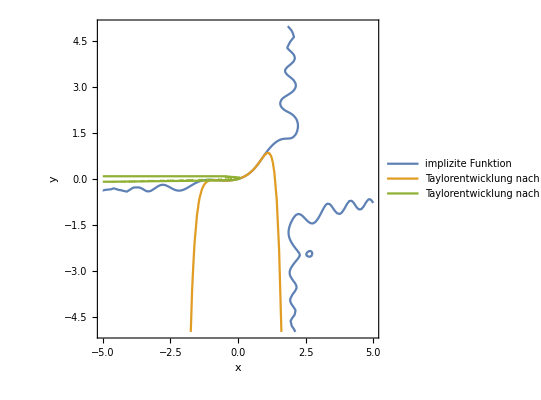

```mathematica
Show[ContourPlot[{Sin[x^2]+2x*y+Cos[y^2]+x-4y==1,taylory10==y,x==taylorx10},{x,-5,5},{y,-5,5},FrameLabel->{"x","y"},PlotLegends->{"implizite Funktion","Taylorentwicklung nach y[x]","Taylorentwicklung nach x[y]"}]]
```